```mathematica
kf1[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Print["D factor;","  diff btn dispersion and omm energy"];
{Dphase1[θ_]=1 +e {0,0,B}.bc1[θ],s v0 kf1[θ]-(B e sm v0 Cos[θ])/kf1[θ]}//FullSimplify
```

D factor;  diff btn dispersion and omm energy

{1-(4 B e s v0^2 Cos[θ])/((μ+√(μ^2-2 B e sm v0^2 Cos[θ]))^2),1/2 ((-2+s) μ+(2+s) √(μ^2-2 B e sm v0^2 Cos[θ]))}

```mathematica
Series[1/(1-(4 B e s v0^2 Cos[θ])/((μ+√(μ^2-2 B e sm v0^2 Cos[θ]))^2)),{B,0,2}]//FullSimplify
```

1+(4 e s v0^2 Cos[θ] B)/((μ+√(μ^2))^2)+(e^2 s v0^4 (2 s √(μ^2)+sm (μ+√(μ^2))) Cos[θ]^2 B^2)/(μ^4 (μ+√(μ^2)))+O[B]^3

{1./(1.-(7.2×10^-7 B)/((0.1+√(0.01-1.26×10^-6 B))^2)),1.+0.000018 B+1.458×10^-9 B^2,0.5 (-0.15+2.5 √(0.01-1.26×10^-6 B))}

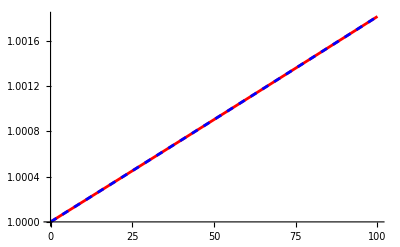

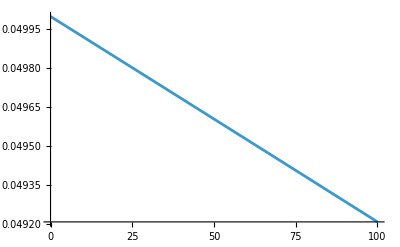

```mathematica
s=1/2;sm=7/4;(*s=3/2;sm=3/4;*)e=1;v0=6 10^-4;μ=0.1;θ=0;
{f1=1.0/(1-(4 B e s v0^2 Cos[θ])/((μ+√(μ^2-2 B e sm v0^2 Cos[θ]))^2)),f2=1+(4 e s v0^2 Cos[θ] B)/(2μ)^2+(e^2 s v0^4 (2 s √(μ^2)+sm (μ+√(μ^2))) Cos[θ]^2 B^2)/(μ^4 (2μ)),f3=1/2 ((-2+s) μ+(2+s) √(μ^2-2 B e sm v0^2 Cos[θ]))}//N
Plot[{f1,f2},{B,0,100},PlotStyle->{Directive[Red],Directive[Blue,Dashed]}]
Plot[f3,{B,0,100}]
Clear[s,θ,e,sm,v0,μ,kf1];
```

## sigma

```mathematica
Clear[sig,s,μ,B,v0];
sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);(* -Graphics-*);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(-  sm B e v0)/( kf1[θ])^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0 (s-(B e sm Cos[θ])/kf1[θ]^2) kf1[θ];
(* -Graphics-*)
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]-(B e sm v0 Cos[2 θ])/kf1[θ]^2+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]=(-  sm B e v0)/kf2[θ]^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk2[θ_]=v0 (s-(B e sm Cos[θ])/kf2[θ]^2) kf2[θ];
h2[θ_]=1/Dphase2[θ]( s v0 Cos[θ]-(B e sm v0 Cos[2 θ])/kf2[θ]^2+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])) );

(* ***************************** *)

τ1[θ_]=(βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}])^-1;
(**************) 

τ2[θ_]=(βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+

+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2,s1+s2(*,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol0],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol1],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol2]*)}
];
(* sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
	(*mu=10.0^-1;v0val= 6 10^-4;in=1;
	Quiet[sig[0.01,mu,v0val,{in,in,0.5 in}]]
	Quiet[sig[-0.01,mu,v0val,{in,in,0.5 in}]]
	Quiet[sig[0.00000001,mu,v0val,{in,in,0.5 in}]]
Quiet[sig0[mu,v0val,{in,in,0.5 in}]]*)
```

## sigma at B=0

```mathematica
Clear[sig0,s,μ,B,v0];
sig0[μ_,v0_,{βintra11_,βintra33_,βinter_}]:=Block[{e=1,B=0,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ] );
(*****************)

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=μ/v0;
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 ;
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=v0 s kf2[θ];
h2[θ_]=(s v0 Cos[θ])/Dphase2[θ];

(* ***************************** *)

τ1[θ_]=(βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(3βinter)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}])^-1;
(**************) 

τ2[θ_]=(βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+

+(3βinter)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{3 hctsq2 βinter+3 hzero2 βinter-3 hctsq1 βintra11+5 hzero1 βintra11}, {-3 hct2 βinter+9 hctcube2 βinter+17 hct1 βintra11-27 hctcube1 βintra11}, {-9 hctsq2 βinter+3 hzero2 βinter+9 hctsq1 βintra11-3 hzero1 βintra11}, {9 hct2 βinter-15 hctcube2 βinter-27 hct1 βintra11+45 hctcube1 βintra11}, {3 hctsq1 βinter+3 hzero1 βinter-3 hctsq2 βintra33+5 hzero2 βintra33}, {-3 hct1 βinter+9 hctcube1 βinter+9 hct2 βintra33-3 hctcube2 βintra33}, {-9 hctsq1 βinter+3 hzero1 βinter+9 hctsq2 βintra33-3 hzero2 βintra33}, {9 hct1 βinter-15 hctcube1 βinter-3 hct2 βintra33+5 hctcube2 βintra33}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, 3 ctquad1 βintra11-5 ctsq1 βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11, -3 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter-3 ctcube2 βinter, -3 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter-3 ctfive2 βinter}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11, 3 ct2 βinter-9 ctcube2 βinter, -9 ctquad2 βinter+3 ctsq2 βinter, 3 ctcube2 βinter-9 ctfive2 βinter, 3 ctquad2 βinter-9 ctsix2 βinter}, {-9 ctsq1 βintra11+3 zero1 βintra11, 3 ct1 βintra11-9 ctcube1 βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 ctcube1 βintra11-9 ctfive1 βintra11, 9 ctsq2 βinter-3 zero2 βinter, -3 ct2 βinter+9 ctcube2 βinter, 9 ctquad2 βinter-3 ctsq2 βinter, -3 ctcube2 βinter+9 ctfive2 βinter}, {27 ct1 βintra11-45 ctcube1 βintra11, -45 ctquad1 βintra11+27 ctsq1 βintra11, 27 ctcube1 βintra11-45 ctfive1 βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11, -9 ct2 βinter+15 ctcube2 βinter, 15 ctquad2 βinter-9 ctsq2 βinter, -9 ctcube2 βinter+15 ctfive2 βinter, -9 ctquad2 βinter+15 ctsix2 βinter}, {-3 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter-3 ctcube1 βinter, -3 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter-3 ctfive1 βinter, 1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, 3 ctquad2 βintra33-5 ctsq2 βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 ct1 βinter-9 ctcube1 βinter, -9 ctquad1 βinter+3 ctsq1 βinter, 3 ctcube1 βinter-9 ctfive1 βinter, 3 ctquad1 βinter-9 ctsix1 βinter, -9 ct2 βintra33+3 ctcube2 βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, -9 ctcube2 βintra33+3 ctfive2 βintra33, -9 ctquad2 βintra33+3 ctsix2 βintra33}, {9 ctsq1 βinter-3 zero1 βinter, -3 ct1 βinter+9 ctcube1 βinter, 9 ctquad1 βinter-3 ctsq1 βinter, -3 ctcube1 βinter+9 ctfive1 βinter, -9 ctsq2 βintra33+3 zero2 βintra33, 3 ct2 βintra33-9 ctcube2 βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-9 ctfive2 βintra33}, {-9 ct1 βinter+15 ctcube1 βinter, 15 ctquad1 βinter-9 ctsq1 βinter, -9 ctcube1 βinter+15 ctfive1 βinter, -9 ctquad1 βinter+15 ctsix1 βinter, 3 ct2 βintra33-5 ctcube2 βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, 3 ctcube2 βintra33-5 ctfive2 βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ1,a1,b1,c1,λ2,a2,b2,c2};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1)+(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,(*matr[[3]]+colvec[[3]]==0,*)matr[[4]]+colvec[[4]]==0,matr[[5]]+colvec[[5]]==0,matr[[6]]+colvec[[6]]==0,matr[[7]]+colvec[[7]]==0,matr[[8]]+colvec[[8]]==0,cs==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2,s1+s2(*,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol0],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol1],MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol2]*)}
];
(* sig0[μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
(*mu=10.0^-1;v0val= 6 10^-4;in=1;
Quiet[sig0[mu,v0val,{in,in,0.5 in}]]*)
```

## data

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.1;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-45,45,10}]]]
```

{0,1.84368×10^-8,-5.4885×10^-7,-5.30413×10^-7}

{{-45,1.84476×10^-8,-5.48856×10^-7,-5.30408×10^-7},{-35,1.84433×10^-8,-5.48853×10^-7,-5.3041×10^-7},{-25,1.84401×10^-8,-5.48852×10^-7,-5.30411×10^-7},{-15,1.8438×10^-8,-5.4885×10^-7,-5.30412×10^-7},{-5,1.84369×10^-8,-5.4885×10^-7,-5.30413×10^-7},{0,1.84368×10^-8,-5.4885×10^-7,-5.30413×10^-7},{5,1.84369×10^-8,-5.4885×10^-7,-5.30413×10^-7},{15,1.8438×10^-8,-5.4885×10^-7,-5.30412×10^-7},{25,1.84401×10^-8,-5.48852×10^-7,-5.30411×10^-7},{35,1.84433×10^-8,-5.48853×10^-7,-5.3041×10^-7},{45,1.84476×10^-8,-5.48856×10^-7,-5.30408×10^-7}}

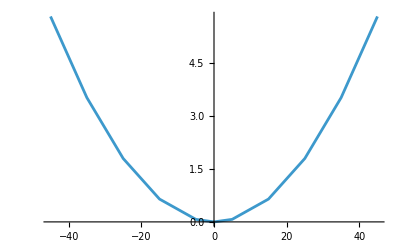

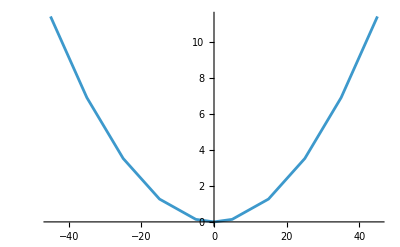

```mathematica
len=Length[list];
{x1,x2}={1/x[[2]],1/x[[3]]};
dat01=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat02=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat01]
ListLinePlot[dat02]
```

{0,8.03626×10^-9,1.68675×10^-7,1.76711×10^-7}

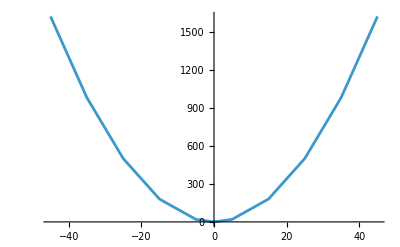

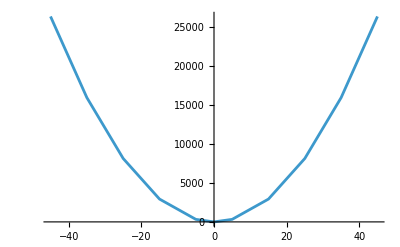

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.00006;
x=Quiet[sig0[mu,v0val,{in,in,rat in}]]
list=Sort[Join[{x},Table[Quiet[sig[B,mu,v0val,{in,in,rat in}]],{B,-45,45,10}]]];
len=Length[list];
{x1,x2}={1/x[[2]],1/x[[3]]};
dat01=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
dat02=Table[{list[[i,1]],(Re[list[[i,3]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat01]
ListLinePlot[dat02]
```